```mathematica
decilPorcentajes = Import["/home/erasmo/Escritorio/proyecto_MinData_SNPs/dataviz_snp/codes/decile_risk.csv","CSV"];
decilPorcentajes =decilPorcentajes[[2;;11,All]];
```

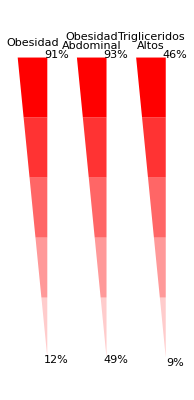

```mathematica
plantillaRiesgo ={Red, Opacity[0.2],Polygon[{{0.2,0},{0.2,0.2},{0.18,0.2}}],
Opacity[0.4],
Polygon[{{0.2,0.2},{0.2,0.4},{0.16,0.4},{0.18,0.2}}],
Opacity[0.6],
Polygon[{{0.2,0.4},{0.2,0.6},{0.14,0.6},{0.16,0.4}}],
Opacity[0.8],
Polygon[{{0.2,0.6},{0.2,0.8},{0.12,0.8},{0.14,0.6}}],
Opacity[1],
Polygon[{{0.2,0.8},{0.2,1},{0.10,1},{0.12,0.8}}],
Black,Text["Obesidad",{0.15,1.05}],
Text[ToString[Round[decilPorcentajes[[10,3]]]]<>"%",{0.23,1.01}],
Text[ToString[Round[decilPorcentajes[[1,3]]]]<>"%",{0.23,-0.01}],
Red, Opacity[0.2],
Polygon[{{0.4,0},{0.4,0.2},{0.38,0.2}}],
Opacity[0.4],
Polygon[{{0.4,0.2},{0.4,0.4},{0.36,0.4},{0.38,0.2}}],
Opacity[0.6],
Polygon[{{0.4,0.4},{0.4,0.6},{0.34,0.6},{0.36,0.4}}],
Opacity[0.8],
Polygon[{{0.4,0.6},{0.4,0.8},{0.32,0.8},{0.34,0.6}}],
Opacity[1],
Polygon[{{0.4,0.8},{0.4,1},{0.30,1},{0.32,0.8}}],
Black,Text["Obesidad",{0.35,1.07}],Text["Abdominal",{0.35,1.04}],
Text[ToString[Round[decilPorcentajes[[10,4]]]]<>"%",{0.43,1.01}],
Text[ToString[Round[decilPorcentajes[[1,4]]]]<>"%",{0.43,-0.01}],
Red, Opacity[0.2],Polygon[{{0.6,0},{0.6,0.2},{0.58,0.2}}],
Opacity[0.4],
Polygon[{{0.6,0.2},{0.6,0.4},{0.56,0.4},{0.58,0.2}}],
Opacity[0.6],
Polygon[{{0.6,0.4},{0.6,0.6},{0.54,0.6},{0.56,0.4}}],
Opacity[0.8],
Polygon[{{0.6,0.6},{0.6,0.8},{0.52,0.8},{0.54,0.6}}],
Opacity[1],
Polygon[{{0.6,0.8},{0.6,1},{0.50,1},{0.52,0.8}}],
Black,Text["Trigliceridos",{0.55,1.07}],Text["Altos",{0.55,1.04}],
Text[ToString[Round[decilPorcentajes[[10,5]]]]<>"%",{0.63,1.01}],
Text[ToString[Round[decilPorcentajes[[1,5]]]]<>"%",{0.63,-0.02}]
};
Graphics[plantillaRiesgo]
```

```mathematica
data = Import["/home/erasmo/Escritorio/proyecto_MinData_SNPs/dataviz_snp/codes/db_viz_deciles_test.csv","CSV"];
test =data[[2]];
test[[15;;17]];
```

```mathematica
color1 = RGBColor[1.,0.92,0.62];
color2 = RGBColor[0.62,0.72,1.];
color3 = RGBColor[1.,0.6,0.7];
```

```mathematica
Do[
paciente = data[[i]];
ID = paciente[[2]];
enfermo = paciente[[6;;8]];
deciles = paciente[[9;;11]];
SNPs = paciente[[12;;14]];
ancestria = paciente[[15;;17]];
anguloAncestria = {ancestria[[1]]*2*Pi,
Total[ancestria[[1;;2]]]*2*Pi,
Total[ancestria]*2*Pi};
posicionDeciles = (deciles - 1) /10;

plantillaAncestria ={LightGray,Annulus[{1,0.8},{0.10,0.23}],
color1,Annulus[{1,0.8},{0.11,0.22},{0,anguloAncestria[[1]]}],
color2,Annulus[{1,0.8},{0.11,0.22},{anguloAncestria[[1]],anguloAncestria[[2]]}],
color3,Annulus[{1,0.8},{0.11,0.22},{anguloAncestria[[2]],anguloAncestria[[3]]}],
Black,Text[Style["Ancestría",Large],{1.45,1}],
Text["EUROPEO: "<>ToString[ancestria[[1]]* 100]<>"%",{1.45,0.85},Background-> color1],
Text["AMERICANO: "<>ToString[ancestria[[2]]* 100]<>"%",{1.45,0.8},Background->color2],
Text["AFRICANO: "<>ToString[ancestria[[3]]* 100]<>"%",{1.45,0.75},Background-> color3]
};
indicadorRiesgo = {
Triangle[{{0.2,0.05 + posicionDeciles[[1]]},{0.27,0.03+ posicionDeciles[[1]]},{0.27,0.07+ posicionDeciles[[1]]}}],
Triangle[{{0.4,0.05+ posicionDeciles[[2]]},{0.47,0.03+ posicionDeciles[[2]]},{0.47,0.07+ posicionDeciles[[2]]}}],
Triangle[{{0.6,0.05+ posicionDeciles[[3]]},{0.67,0.03+ posicionDeciles[[3]]},{0.67,0.07+ posicionDeciles[[3]]}}],
Text[ToString[Round[decilPorcentajes[[1+posicionDeciles[[1]]*10,3]]]]<>"%",{0.25,0.015+ posicionDeciles[[1]]}],
Text[ToString[Round[decilPorcentajes[[1+posicionDeciles[[2]]*10,4]]]]<>"%",{0.45,0.015+ posicionDeciles[[2]]}],
Text[ToString[Round[decilPorcentajes[[1+posicionDeciles[[3]]*10,5]]]]<>"%",{0.65,0.015+ posicionDeciles[[3]]}]
};
separacion = {Thick,Dashed,Line[{{0.7,1.1},{0.7,0}}],Line[{{0.72,0.5},{1.9,0.5}}]};
variantesRiesgo = {
Text[Style["OBESIDAD: "<>ToString[SNPs[[1]]]<>" de 13 variantes de riesgo ",Medium],{1.3,0.3}],
Text[Style["OBESIDAD ABDOMINAL: "<>ToString[SNPs[[2]]]<>" de 9 variantes de riesgo ",Medium],{1.3,0.2}],
Text[Style["TRIGLICERIDOS ALTOS: "<>ToString[SNPs[[3]]]<>" de 9 variantes de riesgo ",Medium],{1.3,0.1}]
};



dv = Graphics[{plantillaRiesgo,indicadorRiesgo,separacion,plantillaAncestria,variantesRiesgo},ImageSize->Large];
fileName = "/home/erasmo/Escritorio/proyecto_MinData_SNPs/dataviz_snp/images/DataViz_P"<>ToString[ID]<>".png";

Export[fileName,dv,"PNG",ImageResolution -> 100];
,{i,2,Length[data],1}]
```